```mathematica
Exit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/2nd_GW_QCD/NANOGrav/num

```mathematica
Mpl=2.435 10^18;
c=299792458 ;(*m/s*)
KinGeV=1/(1.160451812 10^4) 10^(-9)
Mpcinm=3.08568 10^22;
GeVinminv=10^9/(1.97327 10^(-7))
GeVinMpcinv=GeVinminv Mpcinm
MpcinvinHz=1/Mpcinm c
yrins=365.2425 24 60 60
```

8.61733×10^-14

5.06773×10^15

1.56374×10^38

9.7156×10^-15

3.1557×10^7

```mathematica
1/yrins
```

3.16887×10^-8

```mathematica
Or0h2=4.2 10^-5;
h2=0.674^2;
```

### background

```mathematica
ai={1,1.11724,3.12672 10^(-1),-4.68049 10^(-2),-2.65004 10^(-2),-1.19760 10^(-3),1.82812 10^(-4),1.36436 10^(−4),8.55051 10^(−5),1.22840 10^(−5),3.82259 10^(-7),−6.87035 10^(−9)};
bi={1.43382 10^(−2),1.37559 10^(−2),2.92108 10^(−3),−5.38533 10^(−4),−1.62496 10^(−4),−2.87906 10^(−5),−3.84278 10^(−6),2.78776 10^(−6),7.40342 10^(−7),1.17210 10^(−7),3.72499 10^(−9),−6.74107 10^(−11)};
ci={1,6.07869 10^(−1),−1.54485 10^(−1),−2.24034 10^(−1),−2.82147 10^(−2),2.90620 10^(−2),6.86778 10^(−3),−1.00005 10^(−3),−1.69104 10^(−4),1.06301 10^(−5),1.69528 10^(−6),−9.33311 10^(−8)};
di={7.07388 10,9.18011 10,3.31892 10,−1.39779,−1.52558,−1.97857 10^(−2),−1.60146 10^(−1),8.22615 10^(−5),2.02651 10^(−2),−1.82134 10^(−5),7.83943 10^(−5),7.13518 10^(−5)};
```

```mathematica
rhofactor[T_]=0.01Exp[-(Log10[T])^2/2^2];
sfactor[T_]=-0.01Exp[-(Log10[T])^2/2^2];
```

```mathematica
grhohigh[T_]=Sum[ai[[i]]Log[T]^(i-1),{i,12}]/Sum[bi[[i]]Log[T]^(i-1),{i,12}];
gshigh[T_]=grhohigh[T]/(1+Sum[ci[[i]]Log[T]^(i-1),{i,12}]/Sum[di[[i]]Log[T]^(i-1),{i,12}]);
```

```mathematica
rhohigh[T_]=π^2/30 grhohigh[T] T^4;
shigh[T_]=2π^2/45 gshigh[T] T^3;
phigh[T_]=Simplify[T shigh[T]-rhohigh[T]];
```

```mathematica
Sfit[x_]=1+7/4 Exp[−1.0419x](1+1.034x+0.456426x^2+0.0595249x^3);
frho[x_]=Exp[−1.04855x](1+1.03757x+0.508630x^2+0.0893988x^3);
brho[x_]=Exp[−1.03149x](1+1.03317x+0.398264x^2+0.0648056x^3);
fs[x_]=Exp[−1.04190x](1+1.03400x+0.456426x^2+0.0595248x^3);
bs[x_]=Exp[−1.03365x](1+1.03397x+0.342548x^2+0.0506182x^3);
```

```mathematica
me=511 10^(-6);
mmu=0.1056;
mpi0=0.13;
mpipm=0.140;
m1=0.5;
m2=0.77;
m3=1.2;
m4=2;
```

```mathematica
Tnu[T_]=(4/11)^(1/3) Sfit[me/T]^(1/3) T;
```

```mathematica
grhogammalow[T_]=2.030+3.495frho[me/T]+3.446frho[mmu/T]+1.05brho[mpi0/T]+2.08brho[mpipm/T]+4.165brho[m1/T]+30.55brho[m2/T]+89.4brho[m3/T]+8209brho[m4/T];
gsgammalow[T_]=2.008+3.442fs[me/T]+3.468fs[mmu/T]+1.034bs[mpi0/T]+2.068bs[mpipm/T]+4.16bs[m1/T]+30.55bs[m2/T]+90bs[m3/T]+6209bs[m4/T];
grhonulow[T_]=1.353Sfit[me/T]^(4/3);
gsnulow[T_]=1.923Sfit[me/T];
```

```mathematica
rhogammalow[T_]=π^2/30 grhogammalow[T] T^4;
sgammalow[T_]=2π^2/45 gsgammalow[T] T^3;
rhonulow[T_]=π^2/30 grhonulow[T] T^4;
snulow[T_]=2π^2/45 gsnulow[T] T^3;
pgammalow[T_]=Simplify[T sgammalow[T]-rhogammalow[T]];
pnulow[T_]=Simplify[Tnu[T] snulow[T]-rhonulow[T]];
rholow[T_]=Simplify[rhogammalow[T]+rhonulow[T]];
plow[T_]=Simplify[pgammalow[T]+pnulow[T]];
```

```mathematica
Tth=0.12;
```

```mathematica
grho[T_]:=grhohigh[T]/;T>=Tth
grho[T_]:=grhogammalow[T]+grhonulow[T]/;T<Tth
grhop[T_]:=grhohigh'[T]/;T>=Tth
grhop[T_]:=grhogammalow'[T]+grhonulow'[T]/;T<Tth
gs[T_]:=gshigh[T]/;T>=Tth
gs[T_]:=gsgammalow[T]+gsnulow[T]/;T<Tth
```

```mathematica
PETERRIVER=RGBColor["#3498DB"]
```

RGBColor[0.20392156862745098, 0.596078431372549, 0.8588235294117647]

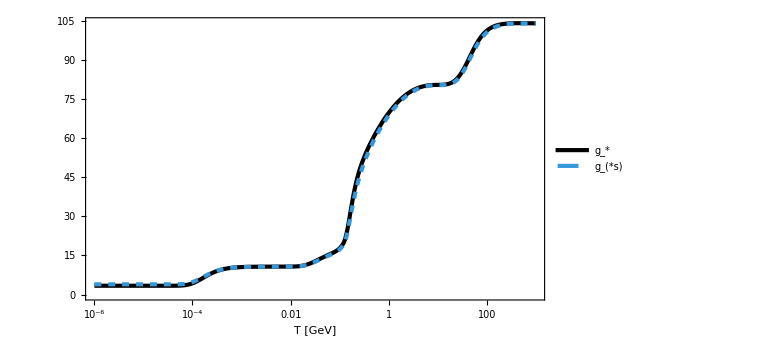

```mathematica
Figgs=LogLinearPlot[{grho[T],gs[T]},{T,10^(-6),10^3},FrameLabel->{Row[{T," [GeV]"}],None},PlotStyle->{{AbsoluteThickness[3],Black},{PETERRIVER,Dashed,AbsoluteThickness[3]}},PlotLegends->Placed[{SubStar[g],Subscript[g, "*s"]},{0.2,0.8}]]//Quiet
```

```mathematica
rho[T_]:=rhohigh[T]/;T>=Tth
rho[T_]:=rholow[T]/;T<Tth
press[T_]:=phigh[T]/;T>=Tth
press[T_]:=plow[T]/;T<Tth
```

```mathematica
EoSw[T_]=press[T]/rho[T];
cs2[T_]:=phigh'[T]/rhohigh'[T]/;T>=Tth
cs2[T_]:=plow'[T]/rholow'[T]/;T<Tth
```

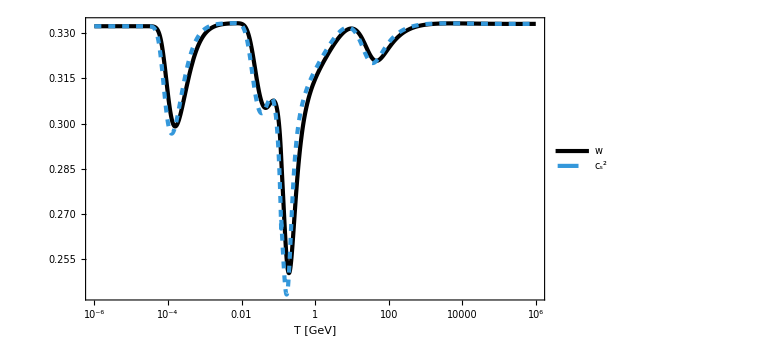

```mathematica
Figwcs=LogLinearPlot[{EoSw[T],cs2[T]},{T,10^-6,10^6},PlotRange->Full,PlotStyle->{{AbsoluteThickness[3],Black},{PETERRIVER,Dashed,AbsoluteThickness[3]}},FrameLabel->{Row[{T," [GeV]"}],None},PlotLegends->Placed[{w,Subscript["c", s]^2},{0.2,0.2}],GridLines->{None,{1/3}}]//Quiet
```

```mathematica
grho0=grho[10^(-6)]//Quiet
gs0=gs[10^(-6)]//Quiet
T0=2.725 KinGeV
```

3.383

3.931

2.34822×10^-13

```mathematica
calH[scalea_,T_]=scalea Sqrt[rho[T]/3/Mpl^2] GeVinMpcinv; (*Mpc^-1*)
calHP[scalea_,T_]=scalea Sqrt[rhoP[T]/3/Mpl^2] GeVinMpcinv; (*Mpc^-1*)
calHM[scalea_,T_]=scalea Sqrt[rhoM[T]/3/Mpl^2] GeVinMpcinv;(*Mpc^-1*)
```

```mathematica
Ti=10^6;
ai=(gs0/gs[Ti])^(1/3) T0/Ti//Quiet
etai=1/calH[ai,Ti]
```

7.86804×10^-20

5.84589×10^-14

```mathematica
etaf=10;
```

```mathematica
bgsol=NDSolve[{T'[eta]==-3(1+EoSw[T[eta]])calH[scalea[eta],T[eta]] grho[T[eta]]/(grhop[T[eta]]+4grho[T[eta]]/T[eta]),scalea'[eta]==scalea[eta]calH[scalea[eta],T[eta]],T[etai]==Ti,scalea[etai]==ai},{T[eta],scalea[eta]},{eta,etai,etaf},WorkingPrecision->30][[1]]//Quiet;//AbsoluteTiming
```

{3.43994,Null}

```mathematica
Tsol[eta_]=T[eta]/. bgsol;
asol[eta_]=scalea[eta]/. bgsol;
```

```mathematica
norm=Tsol[etaf]/T0 asol[etaf]//Quiet
anorm[eta_]=asol[eta/norm]/norm;
Tnorm[eta_]=Tsol[eta/norm];
calHnorm[eta_]=calH[anorm[eta],Tnorm[eta]];
af=anorm[norm etaf]//Quiet;
calHf=calHnorm[norm etaf]//Quiet;
```

0.989259

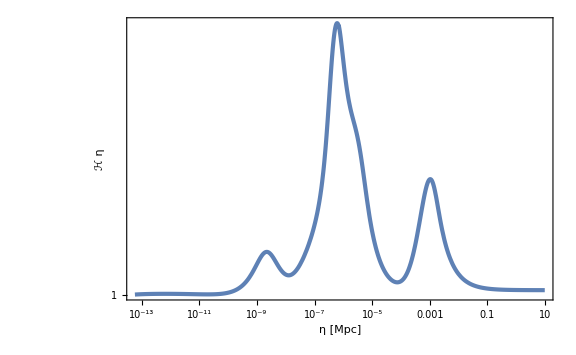

```mathematica
LogLogPlot[{eta calHnorm[eta]},{eta,norm etai,norm etaf},PlotRange->Full,FrameLabel->{"η [Mpc]",η ℋ}]
```

```mathematica
EoSwsol[eta_]=EoSw[Tnorm[eta]];
cs2sol[eta_]:=cs2[Tnorm[eta]];
grhosol[eta_]=grho[Tnorm[eta]];
gssol[eta_]=gs[Tnorm[eta]];
```

```mathematica
anormList=Table[{10^logeta,anorm[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
aint[eta_]=Interpolation[anormList][eta];
calHList=Table[{10^logeta,calHnorm[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
calHint[eta_]=Interpolation[calHList][eta];
EoSwList=Table[{10^logeta,EoSwsol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
cs2List=Table[{10^logeta,cs2sol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
EoSwint[eta_]=Interpolation[EoSwList][eta];
cs2int[eta_]=Interpolation[cs2List][eta];
grhoList=Table[{10^logeta,grhosol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
gsList=Table[{10^logeta,gssol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
grhoint[eta_]=Interpolation[grhoList][eta];
gsint[eta_]=Interpolation[gsList][eta];
```

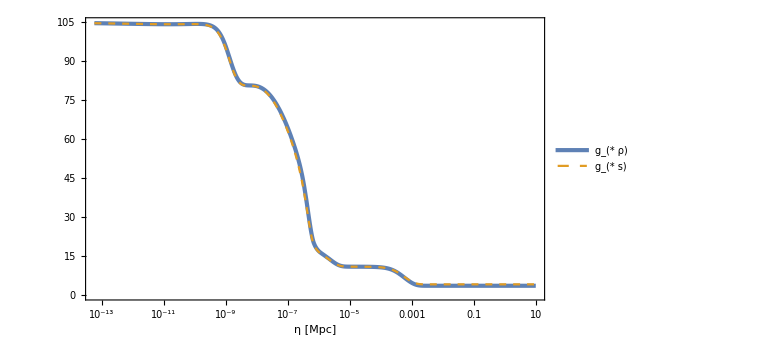

```mathematica
LogLinearPlot[{grhoint[eta],gsint[eta]},{eta,etai,etaf},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[{Subscript[g,"*"ρ],Subscript[g,"*"s]},{0.8,0.8}],FrameLabel->{"η [Mpc]",None}]
```

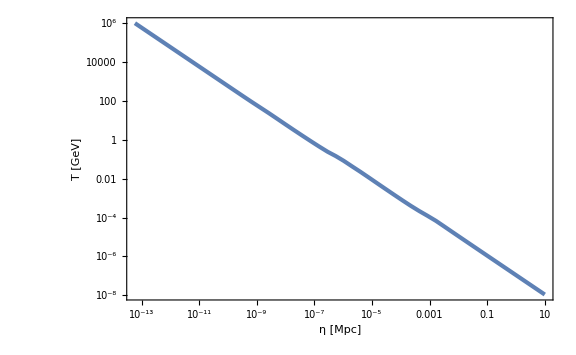

```mathematica
Tvseta=LogLogPlot[{Tsol[eta]},{eta,etai,etaf},FrameLabel->{Row[{η," [Mpc]"}],Row[{T," [GeV]"}]}]
```

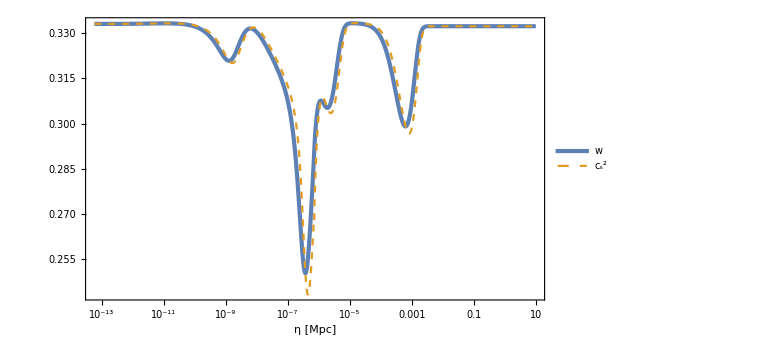

```mathematica
LogLinearPlot[{EoSwint[eta],cs2int[eta]},{eta,etai,etaf},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{Row[{η," [Mpc]"}],None},PlotLegends->Placed[{w,Subscript["c", s]^2},{0.2,0.2}]]//Quiet
```

### scalar

```mathematica
(*xi=10^-2;*)
xf=1000;
```

```mathematica
kmin=10^5;
dk=kmin;
kmax=10^8;
```

```mathematica
PhiList[eta_]=ParallelTable[{(*k=10^logk;*)k,ptbsol=NDSolve[{Phi''[eta]+3calHint[eta](1+cs2int[eta]) Phi'[eta]+(cs2int[eta]k^2+3calHint[eta]^2(cs2int[eta]-EoSwint[eta]))Phi[eta]==0,Phi[etai]==1,Phi'[etai]==0},Phi[eta],{eta,norm etai,xf/k},(*WorkingPrecision->30,*)MaxSteps->10^5][[1]];
Phi[eta]/. ptbsol},(*{logk,(*4*)5,10,10^-2}*){k,kmin,kmax,dk}];//AbsoluteTiming
Clear[k];
```

{24.1646,Null}

```mathematica
PhipList[eta_]=ParallelTable[{PhiList[eta][[i,1]],D[PhiList[eta][[i,2]],eta]},{i,Length[PhiList[eta]]}];
```

```mathematica
calPList[x_]=ParallelTable[{k=PhiList[x/k][[i,1]];k,PhiList[x/k][[i,2]]^2+PhipList[x/k][[i,2]]^2/k^2/cs2int[x/k]},{i,Length[PhiList[x]]}];//AbsoluteTiming
Clear[k];
```

{17.7543,Null}

```mathematica
PhiRad[x_]=9/x^2 (Sin[x/Sqrt[3]]/(x/Sqrt[3])-Cos[x/Sqrt[3]]);
calPRad[x_]=PhiRad[x]^2+PhiRad'[x]^2/(1/3);
NormcalP8=calPList[8].DiagonalMatrix[{1,calPRad[8]^(-1)}];
```

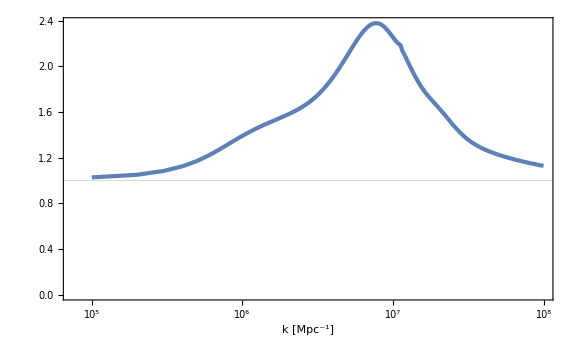

```mathematica
FigScalarAverage=ListLogLinearPlot[{NormcalP8},GridLines->{None,{1}},FrameLabel->{{None,None},{Row[{k," [",Superscript[Mpc,-1],"]"}],k η==8}}]
```

### GW

```mathematica
xi=10^-2;
xf=1000;
```

```mathematica
Clear[k];
G1List[eta_]=ParallelTable[(*k=10^logk;*)
ptbsol=NDSolve[{G''[eta]+(k^2-(1-3EoSwint[eta])/2*calHint[eta]^2)G[eta]==0,G[xi/k]==1,G'[xi/k]==0},G[eta],{eta,xi/k,xf/k},MaxSteps->10^6
(*,WorkingPrecision->10*)(*,AccuracyGoal->10*),PrecisionGoal->10][[1]];
{k,G[eta]/.ptbsol},(*{logk,(*4*)5,10,10^-2}*){k,kmin,kmax,dk}];//AbsoluteTiming
G2List[eta_]=ParallelTable[(*k=10^logk;*)
ptbsol=NDSolve[{G''[eta]+(k^2-(1-3EoSwint[eta])/2*calHint[eta]^2)G[eta]==0,G'[xi/k]==k,G[xi/k]==0},G[eta],{eta,xi/k,xf/k},MaxSteps->10^6
(*,WorkingPrecision->10*)(*,AccuracyGoal->10*),PrecisionGoal->10][[1]];
{k,G[eta]/.ptbsol},(*{logk,(*4*)5,10,10^-2}*){k,kmin,kmax,dk}];//AbsoluteTiming
Clear[k];
```

{62.4322,Null}

{60.9313,Null}

InterpolatingFunction::dmval: Input value {2.77073×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

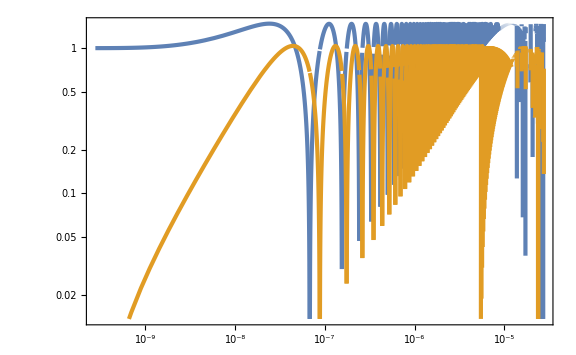

```mathematica
LogLogPlot[{Abs[G1List[eta][[361,2]]],Abs[G2List[eta][[361,2]]]},{eta,xi/G1List[eta][[361,1]],xf/G1List[eta][[361,1]]}]
```

### convolution

```mathematica
kList=Table[PhiList[eta][[i,1]],{i,Length[PhiList[eta]]}];
```

```mathematica
xi=10^-2;
xc=400;
xf=1000;
dx=π;
(*dlogk=10^-2 Log[10];dlogk//N*)
iMax=Length[kList]
```

1000

```mathematica
PhiMode[eta_]=Table[UnitStep[(*eta-xi/kList[[i]],*)xf/kList[[i]]-eta] PhiList[eta][[i,2]],{i,Length[PhiList[eta]]}];
PhipMode[eta_]=Table[UnitStep[(*eta-xi/kList[[i]],*)xf/kList[[i]]-eta] D[PhiMode[eta][[i]],eta],{i,Length[PhiList[eta]]}];
```

```mathematica
G1Mode[eta_]=Table[G1List[eta][[i,2]],{i,Length[G1List[eta]]}];
G1pMode[eta_]=Table[D[G1Mode[eta][[i]],eta],{i,Length[G1Mode[eta]]}];
G2Mode[eta_]=Table[G2List[eta][[i,2]],{i,Length[G2List[eta]]}];
G2pMode[eta_]=Table[D[G2Mode[eta][[i]],eta],{i,Length[G2Mode[eta]]}];
```

```mathematica
ItGen1[i1_,i2_,iGW_,eta_]:=kList[[iGW]] NIntegrate[aint[etap] G1Mode[etap][[iGW]] (2PhiMode[etap][[i1]] PhiMode[etap][[i2]]+4/3/(1+EoSwint[etap]) (PhiMode[etap][[i1]]+PhipMode[etap][[i1]]/calHint[etap]) (PhiMode[etap][[i2]]+PhipMode[etap][[i2]]/calHint[etap])),{etap,xi/kList[[iGW]],eta}
(*,Method->{"GlobalAdaptive","SymbolicProcessing"->0}*)
(*,PrecisionGoal->10*)
(*,WorkingPrecision->50,MaxRecursion->20*)]
ItGen2[i1_,i2_,iGW_,eta_]:=kList[[iGW]] NIntegrate[aint[etap] G2Mode[etap][[iGW]] (2PhiMode[etap][[i1]] PhiMode[etap][[i2]]+4/3/(1+EoSwint[etap]) (PhiMode[etap][[i1]]+PhipMode[etap][[i1]]/calHint[etap]) (PhiMode[etap][[i2]]+PhipMode[etap][[i2]]/calHint[etap])),{etap,xi/kList[[iGW]],eta}
(*,Method->{"GlobalAdaptive","SymbolicProcessing"->0}*)
(*,PrecisionGoal->10*)
(*,WorkingPrecision->50,MaxRecursion->20*)]
ItGen2bar[i_,eta_,ItG1_,ItG2_]:=ItG1^2 (G2Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]^2+G2Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]^2+G2Mode[(kList[[i]]eta)/kList[[i]]][[i]]^2+G2Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]]^2)/4+ItG2^2 (G1Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]^2+G1Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]^2+G1Mode[(kList[[i]]eta)/kList[[i]]][[i]]^2+G1Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]]^2)/4-2 ItG1 ItG2 (G1Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]+G1Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]+G1Mode[(kList[[i]]eta)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta)/kList[[i]]][[i]]+G1Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]])/4
```

```mathematica
ItG1=ItGen1[401,401,401,xc/kList[[401]]];//Quiet//AbsoluteTiming
ItG1
ItG2=ItGen2[401,401,401,xc/kList[[401]]];//Quiet//AbsoluteTiming
ItG2
ItGen2bar[401,xc/kList[[401]],ItG1,ItG2]//Quiet//AbsoluteTiming
```

{0.23977,Null}

5.60068×10^-13

{0.168087,Null}

4.88406×10^-13

{0.045528,1.13879×10^-25}

```mathematica
kyr=1/yrins(2π)/MpcinvinHz
```

2.04934×10^7

```mathematica
iNANOmin=Length[Select[kList MpcinvinHz/(2π),#<2 10^-9&]]
iNANOmax=Length[kList]-Length[Select[kList MpcinvinHz/(2π),#>59 10^-9&]]+1
```

12

382

```mathematica
Table[kList[[i]],{i,iNANOmin,iNANOmax,iNANOmin}]//Length
```

31

```mathematica
kList[[iNANOmin]] MpcinvinHz/(2π)
kList[[iNANOmax]] MpcinvinHz/(2π)
```

1.85554×10^-9

5.90681×10^-8

```mathematica
(*i1step=(*2*)1;
i2step=(*5*)1;*)
(*Di=1000;*)
(*Dup=200;
Ddown=100;
Dlogk1=dlogk i1step;Dlogk1//N
Dlogk2=dlogk i2step;Dlogk2//N*)
(*2Di/istep+1*)
istep[k_]=Floor[k/(10dk)];
Dk[k_]=dk istep[k];
kk=kList[[200]]
istep[kk]
Dk[kk]
Select[Flatten[Table[If[Abs[kList[[i1]]-kList[[i2]]]<=kk<=kList[[i1]]+kList[[i2]],{i1,i2},{0}],{i1,(*Max[300-(*Di*)Ddown,1]*)1,(*Min[300+(*Di*)Dup,iMax]*) iMax,(*i1step*)istep[kk]},{i2,(*Max[300-(*Di*)Ddown,1]*)1,(*Min[300+Di,iMax]*)(*iMax*)i1,(*i2step*)istep[kk]}],1],#[[1]]!=0&]//Length
```

20000000

20

2000000

465

```mathematica
ItG1List=ParallelTable[If[Abs[kList[[i1]]-kList[[i2]]]<=kList[[i]]<=kList[[i1]]+kList[[i2]]&&iNANOmin<=i<=iNANOmax&&Mod[i-iNANOmin,5iNANOmin]==0&&Mod[i1-1,istep[kList[[i]]]]==0&&Mod[i2-1,istep[kList[[i]]]]==0,
ItGen1[i1,i2,i,xc/kList[[i]]]//Quiet,
None],{i,iMax},{i1,iMax},{i2,i1}];//AbsoluteTiming
```

$Aborted

```mathematica
ItG2List=ParallelTable[If[Abs[kList[[i1]]-kList[[i2]]]<=kList[[i]]<=kList[[i1]]+kList[[i2]]&&iNANOmin<=i<=iNANOmax&&Mod[i-iNANOmin,5iNANOmin]==0&&Mod[i1-1,istep[kList[[i]]]]==0&&Mod[i2-1,istep[kList[[i]]]]==0,
ItGen2[i1,i2,i,xc/kList[[i]]]//Quiet,
None],{i,iMax},{i1,iMax},{i2,i1}];//AbsoluteTiming
```

```mathematica
OGWc[i_,eta_,ns_]:=2 8/243 (*Dlogk1 Dlogk2*)Dk[kList[[i]]]^2/(aint[eta]calHint[eta])^2*Sum[If[Abs[kList[[i1]]-kList[[i2]]]<=kList[[i]]<=kList[[i1]]+kList[[i2]],((kList[[i1]]kList[[i2]])/kyr^2)^ns 1/(kList[[i1]]kList[[i2]])(kList[[i1]]^2-(kList[[i]]^2-kList[[i2]]^2+kList[[i1]]^2)^2/4/kList[[i]]^2)^2/kList[[i1]]/kList[[i2]]*ItGen2bar[i,eta,ItGen1[i1,i2,i,eta],ItGen2[i1,i2,i,eta]],0],{i1,(*Max[i-(*Di*)Ddown,1]*)1,(*Min[i+(*Di*)Dup,iMax]*) iMax,istep[kList[[i]]]},{i2,(*Max[i-(*Di*)Ddown,1]*)1,(*Min[i+Di,iMax]*)(*iMax*)i1,istep[kList[[i]]]}]
```

```mathematica
OGW0h2[i_,ns_]:=(aint[xc/kList[[i]]]calHint[xc/kList[[i]]]/af/calHf)^2 Or0h2 OGWc[i,xc/kList[[i]],ns];
```

```mathematica
OGW0h2[200,2]//Quiet//AbsoluteTiming
```

$Aborted

```mathematica
OGW0h2List=ParallelTable[{kList[[i]],OGW0h2[i,1]//Quiet},{i,(*1,iMax*)iNANOmin,iNANOmax,(*20*)5}];//AbsoluteTiming
```

$Aborted

```mathematica
(*OGW0h2ListTrim=Select[OGW0h2List.DiagonalMatrix[{MpcinvinHz/(2π),1}],2 10^-9<#[[1]]<59 10^-9&];*)
```

```mathematica
fit[f_]=A(f yrins)^n/. FindFit[OGW0h2List(*Trim*),A(f yrins)^n,{A,n},f]
```

(1.45122×10^-7)/f^0.266732

8.27628×10^7 f^1.70612

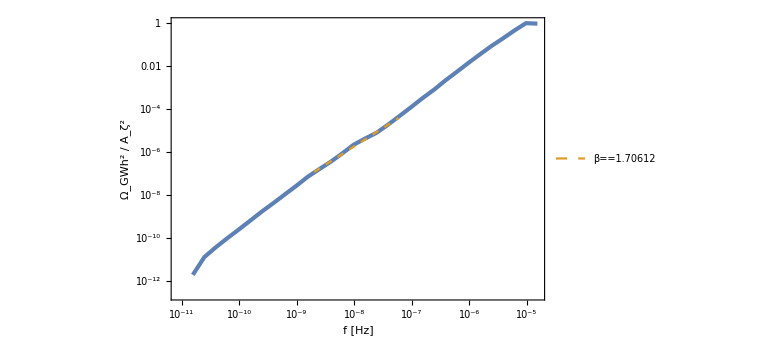

```mathematica
Show[ListLogLogPlot[OGW0h2List.DiagonalMatrix[{MpcinvinHz/(2π),1}],GridLines->{{2 10^-9,59 10^-9},None},FrameLabel->{"f [Hz]","Ω_GWh^2 / A_ζ^2"}],LogLogPlot[fit[f],{f,2 10^-9,59 10^-9},PlotStyle->{Color[2],Dashed},PlotLegends->Placed[{β==n/.FindFit[OGW0h2ListTrim,A(f yrins)^n,{A,n},f]},{0.3,0.2}]]]
```

```mathematica
Log10[2 10^-9]//N
Log10[59 10^-9]//N
```

-8.69897

-7.22915

### NANOGrav

```mathematica
Agamma1sData=Import["Agamma1s.csv"];
Agamma2sData=Import["Agamma2s.csv"];
Agamma3sData=Import["Agamma3s.csv"];
```

```mathematica
Ag1sMean=Mean[Agamma1sData];
Ag2sMean=Mean[Agamma2sData];
Ag3sMean=Mean[Agamma3sData];
```

```mathematica
Ag1sSph=Map[{ArcTan[#[[1]]-Ag1sMean[[1]],#[[2]]-Ag1sMean[[2]]],#[[1]],#[[2]]}&,Agamma1sData];
Ag2sSph=Map[{ArcTan[#[[1]]-Ag2sMean[[1]],#[[2]]-Ag2sMean[[2]]],#[[1]],#[[2]]}&,Agamma2sData];
Ag3sSph=Map[{ArcTan[#[[1]]-Ag3sMean[[1]],#[[2]]-Ag3sMean[[2]]],#[[1]],#[[2]]}&,Agamma3sData];
```

```mathematica
Agamma1sSort=Map[{#[[1]],10^(#[[2]])}&,Sort[Ag1sSph][[All,2;;3]]];
Agamma2sSort=Map[{#[[1]],10^(#[[2]])}&,Sort[Ag2sSph][[All,2;;3]]];
Agamma3sSort=Map[{#[[1]],10^(#[[2]])}&,Sort[Ag3sSph][[All,2;;3]]];
```

```mathematica
Agamma1s=Join[Agamma1sSort,{Agamma1sSort[[1]]}];
Agamma2s=Join[Agamma2sSort,{Agamma2sSort[[1]]}];Agamma3s=Join[Agamma3sSort,{Agamma3sSort[[1]]}];
```

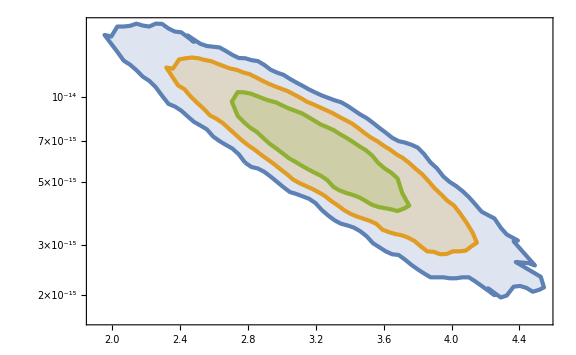

```mathematica
ListLogPlot[{Agamma3s,Agamma2s,Agamma1s},Filling->Bottom]
```

```mathematica
Ωyrh2[A_]=(2π)/3(1/(100 10^3/Mpcinm))^2 A^2 yrins^-2;
β[γ_]=5-γ;
```

```mathematica
Ωbeta1s=Map[{β[#[[1]]],Ωyrh2[#[[2]]]}&,Agamma1s];
Ωbeta2s=Map[{β[#[[1]]],Ωyrh2[#[[2]]]}&,Agamma2s];
Ωbeta3s=Map[{β[#[[1]]],Ωyrh2[#[[2]]]}&,Agamma3s];
```

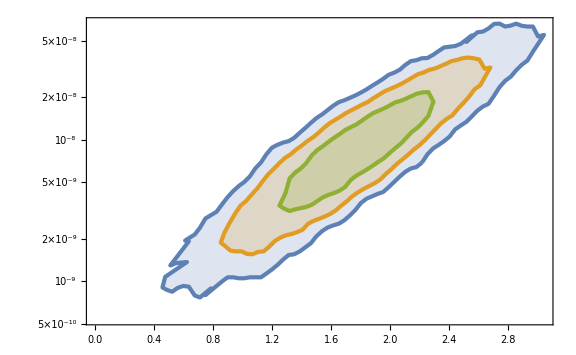

```mathematica
ListLogPlot[{Ωbeta3s,Ωbeta2s,Ωbeta1s},Filling->Bottom]
```

```mathematica
QnsRDList=Transpose[{{0.4,0.6,0.8,1.0,1.2,1.4,1.6,1.8,2.0,2.2,2.4},{0.8196,0.7984,0.7956,0.8222,0.8988,1.074,1.470,2.478,5.783,24.77,708.2}}];
```

```mathematica
QnsRDint[ns_]=Interpolation[QnsRDList,InterpolationOrder->1][ns];
```

```mathematica
I2RDmean[u_,v_]=1/2((3(u^2+v^2-3))/(4 u^3 v^3))^2((-4u v+(u^2+v^2-3)Log[Abs[(3-(u+v)^2)/(3-(u-v)^2)]])^2+π^2(u^2+v^2-3)^2 UnitStep[v+u-Sqrt[3]]);
```

```mathematica
uu[t_,s_]=(t+s+1)/2;
vv[t_,s_]=(t-s+1)/2;
```

```mathematica
OGWh2RD[ns_]:=Or0h2 1/24 2NIntegrate[((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2 I2RDmean[uu[t,s],vv[t,s]] uu[t,s]^(ns-1)vv[t,s]^(ns-1),{t,10^-1,10^7},{s,-1,1},WorkingPrecision->30]
```

```mathematica
OGWh2RDList=ParallelTable[{ns-1,OGWh2RD[ns]//Quiet},{ns,1,3,10^-1}];//AbsoluteTiming
```

{18.1691,Null}

```mathematica
QnsRD[ns_]=10^(aa(ns-1)^2+bb(ns-1)+cc)/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,OGWh2RDList],aa x^2+bb x+cc,{aa,bb,cc},x]
```

10^(-3.80823-3.8552 (-1+ns)+4.06288 (-1+ns)^2)

```mathematica
QnsQCD[ns_]=10^(1.101(ns-1)^2+0.1618(ns-1)-4.931);
```

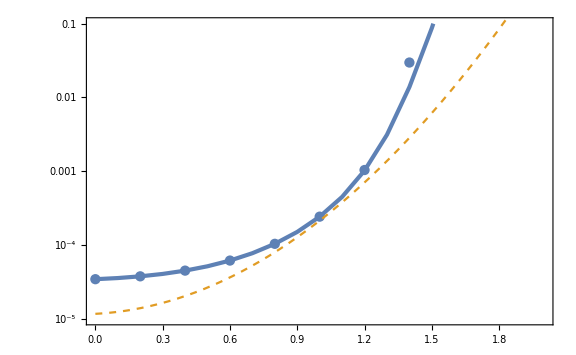

```mathematica
Show[ListLogPlot[OGWh2RDList,PlotRange->{10^-5,0.1}],ListLogPlot[Map[{#[[1]]-1,#[[2]]Or0h2}&,QnsRDList],Joined->False],LogPlot[QnsQCD[nsm1+1],{nsm1,0,2},PlotStyle->{{Color[2],Dashed},{Color[3],Dashed}}]]
```

```mathematica
Export["QnsRD.dat",OGWh2RDList];
```

```mathematica
10^-4.2(10^7)^1.4
```

398107.

```mathematica
AzRD[Oh2_,ns_]=Sqrt[Oh2/QnsRD[ns]];
nsRD[beta_]=beta/2+1;
AzQCD[Oh2_,ns_]=Sqrt[Oh2/QnsQCD[ns]];
nsQCD[beta_]=(beta+0.265)/2.118+1;
```

```mathematica
AnsRD1s=Map[{nsRD[#[[1]]]-1,AzRD[#[[2]],nsRD[#[[1]]]]}&,Ωbeta1s];
AnsRD2s=Map[{nsRD[#[[1]]]-1,AzRD[#[[2]],nsRD[#[[1]]]]}&,Ωbeta2s];
AnsRD3s=Map[{nsRD[#[[1]]]-1,AzRD[#[[2]],nsRD[#[[1]]]]}&,Ωbeta3s];
AnsQCD1s=Map[{nsQCD[#[[1]]]-1,AzQCD[#[[2]],nsQCD[#[[1]]]]}&,Ωbeta1s];
AnsQCD2s=Map[{nsQCD[#[[1]]]-1,AzQCD[#[[2]],nsQCD[#[[1]]]]}&,Ωbeta2s];
AnsQCD3s=Map[{nsQCD[#[[1]]]-1,AzQCD[#[[2]],nsQCD[#[[1]]]]}&,Ωbeta3s];
```

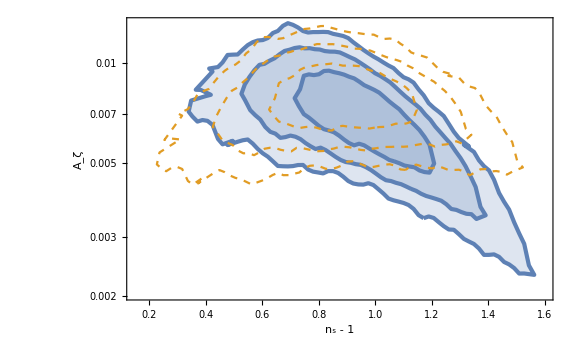

```mathematica
Show[ListLogPlot[{AnsQCD3s,AnsQCD2s,AnsQCD1s},PlotRange->{{0.15,1.6},Automatic}(*{{1.2,2.6},{5 10^-4,0.03}}*),Filling->Bottom,FrameLabel->{"n_(<s>) - 1",Subscript[A, ζ]},PlotStyle->{{AbsoluteThickness[3],Color[1]}}],ListLogPlot[{AnsRD3s,AnsRD2s,AnsRD1s},PlotStyle->{{Dashed,Color[2]}}]]
```

```mathematica
W[z_]=E^(-z^2/2);
```

```mathematica
kyr=1/yrins(2π)/MpcinvinHz
```

2.04934×10^7

```mathematica
16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,∞},Assumptions->{ns>0,R>0}]//Simplify
```

8/81 Az ks (1/(ks R))^ns R Gamma[(3+ns)/2]

```mathematica
δrms[R_]=Sqrt[16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,∞},Assumptions->{ns>0,R>0}]]//Simplify
```

2/9 √2 √(Az ks (1/(ks R))^ns R Gamma[(3+ns)/2])

```mathematica
Msol=1.989 10^33;
```

```mathematica
1/(1.56 10^13)
```

6.41026×10^-14

```mathematica
Rsol=R/.Solve[10^20(50/106.75)^(-1/6)(R 1.56 10^13)^2==Msol,R][[2]]
```

2.68376×10^-7

```mathematica
RinM[M_]=Rsol(M/Ms)^(1/2)
```

2.68376×10^-7 √(M/Ms)

```mathematica
δrms[RinM[Ms]]
```

0.000162807 √((3.72612×10^6)^ns Az (1/ks)^(-1+ns) Gamma[(3+ns)/2])

```mathematica
δrms[RinM[Ms]]/.{ns->2,Az->0.007,ks->kyr}
```

0.0129268